## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
getRegionSAS[sas_]:=And@@(GreaterEqual[#,0]&/@sas);
verifyResults[benchmark_,plot_,plotRange_,verifyTimeLimit_]:= Module[
{systemPath,xvarSet,yvarSet,zvarSet,s1,s2,hPath,hData,h,hHomo,sdpTime,verifyTime,totalTime,result,flag,flagHomo,i},
systemPath=FileNameJoin[{".","Results","problem",StringJoin[benchmark,".txt"]}];
{xvarSet,yvarSet,zvarSet,s1,s2} = ReadList[systemPath];
Print["x Variables: ",xvarSet];
Print["y Variables: ",yvarSet];
Print["z Variables: ",zvarSet];
Print["S1: ",s1];
Print["S2: ",s2];

Print["Verifying results (CAV20 method)..."];
flag =1;
hPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];

(*Length(hData)== 1 if the degree of the template is fixed*)
h = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerify[xvarSet, yvarSet, zvarSet, s1,s2,h],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flag=0;
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["h",h]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[h]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

Print["Verifying results (homogenization)..."];
hPath=FileNameJoin[{".","Results","homo",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];
flagHomo=1;
(*Length(hData)== 1 if the degree of the template is fixed*)
hHomo = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerifyHomo[xvarSet, yvarSet, zvarSet, s1,s2,hHomo],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flagHomo=0
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["hHomo:",hHomo]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[hHomo]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

If[ plot== 1,
If[Length[xvarSet]== 2,myPlot2D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
If[Length[xvarSet]== 3,myPlot3D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
]
]

myVerify [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,h_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[h-1< 0&&s1Cons,Join[xvarSet,yvarSet]];
cond2 =FindInstance[-h-1<0&&s2Cons,Join[xvarSet,zvarSet]];
Print[cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myVerifyHomo [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,hHomo_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[hHomo≤  0&&s1Cons,Join[xvarSet,yvarSet],Reals];
cond2 =FindInstance[-hHomo≤  0&&s2Cons,Join[xvarSet,zvarSet],Reals];
Print[cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]

myPlot2D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
Print[s1Cons];
Print[s2Cons];
Print[h];
Print[hHomo];
(*s1Cons=And@@Thread[GreaterEqualThan[0][s1]];s2Cons=And@@Thread[GreaterEqualThan[0][s2]];*)
s1Plot=RegionPlot[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];

hPlot=RegionPlot[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
]


(*inefficient, use other tools*)
myPlot3D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot3D..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
s1Plot=RegionPlot3D[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot3D[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
hPlot=RegionPlot3D[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot3D[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
];
```

## Benchmarks

### 2-d benchmarks

2d_ex2

x Variables: {x,y}

y Variables: {y0}

z Variables: {z0}

S1: {{11.-x^4+0.1 y^4,y^3,0.91-4. x+6. x^2-4. x^3+x^4+y^4,-0.1025+4. x+6. x^2+4. x^3+x^4+y^4},{-0.0975+4. x-6. x^2+4. x^3-x^4-y^4,0.91-4. x+6. x^2-4. x^3+x^4+y^4,-0.1025+4. x+6. x^2+4. x^3+x^4+y^4},{-0.96-4. x-6. x^2-4. x^3-x^4-y^4}}

S2: {{11.-x^4+0.1 y^4,-y^3,0.91+4. x+6. x^2+4. x^3+x^4+y^4,-0.1025-4. x+6. x^2-4. x^3+x^4+y^4},{-0.0975-4. x-6. x^2-4. x^3-x^4-y^4,0.91+4. x+6. x^2+4. x^3+x^4+y^4,-0.1025-4. x+6. x^2-4. x^3+x^4+y^4},{-0.96+4. x-6. x^2+4. x^3-x^4-y^4}}

Verifying results (CAV20 method)...

{{x→-1.82116,y→0.897145,y0→0.}}{}

Numerical Errors Detected.

SDP Time: 0.228259

verify Time: 0.010911

Total Time: 0.23917

Verifying results (homogenization)...

{}{}

Valid solution.

hHomo:0.0294636 x+0.0000421631 x^2-0.108696 x^3-0.000173171 x^4+0.0289498 x^5+0.0000741783 x^6+0.0077157 x^7-0.00146443 y+0.000111155 x y+0.0530631 x^2 y-0.000380486 x^3 y-0.0876205 x^4 y+0.000155103 x^5 y+0.0313849 x^6 y+0.000031076 y^2-0.0895045 x y^2-0.0000680402 x^2 y^2+0.123661 x^3 y^2+0.0000228717 x^4 y^2-0.0562809 x^5 y^2+0.040397 y^3-0.000186376 x y^3-0.348394 x^2 y^3+0.000325299 x^3 y^3+0.109227 x^4 y^3-0.000190502 y^4+0.496569 x y^4+0.000917235 x^2 y^4+0.401523 x^3 y^4-0.165938 y^5+0.000999477 x y^5+x^2 y^5+0.000379231 y^6+0.0850186 x y^6+0.286855 y^7

SDP Time: 5.752

verify Time: 9.45846

Total Time: 15.2105

Plot2d...

(11.-x^4+0.1 y^4≥0&&y^3≥0&&0.91-4. x+6. x^2-4. x^3+x^4+y^4≥0&&-0.1025+4. x+6. x^2+4. x^3+x^4+y^4≥0)||(-0.0975+4. x-6. x^2+4. x^3-x^4-y^4≥0&&0.91-4. x+6. x^2-4. x^3+x^4+y^4≥0&&-0.1025+4. x+6. x^2+4. x^3+x^4+y^4≥0)||-0.96-4. x-6. x^2-4. x^3-x^4-y^4≥0

(11.-x^4+0.1 y^4≥0&&-y^3≥0&&0.91+4. x+6. x^2+4. x^3+x^4+y^4≥0&&-0.1025-4. x+6. x^2-4. x^3+x^4+y^4≥0)||(-0.0975-4. x-6. x^2-4. x^3-x^4-y^4≥0&&0.91+4. x+6. x^2+4. x^3+x^4+y^4≥0&&-0.1025-4. x+6. x^2-4. x^3+x^4+y^4≥0)||-0.96+4. x-6. x^2+4. x^3-x^4-y^4≥0

-1

0.0294636 x+0.0000421631 x^2-0.108696 x^3-0.000173171 x^4+0.0289498 x^5+0.0000741783 x^6+0.0077157 x^7-0.00146443 y+0.000111155 x y+0.0530631 x^2 y-0.000380486 x^3 y-0.0876205 x^4 y+0.000155103 x^5 y+0.0313849 x^6 y+0.000031076 y^2-0.0895045 x y^2-0.0000680402 x^2 y^2+0.123661 x^3 y^2+0.0000228717 x^4 y^2-0.0562809 x^5 y^2+0.040397 y^3-0.000186376 x y^3-0.348394 x^2 y^3+0.000325299 x^3 y^3+0.109227 x^4 y^3-0.000190502 y^4+0.496569 x y^4+0.000917235 x^2 y^4+0.401523 x^3 y^4-0.165938 y^5+0.000999477 x y^5+x^2 y^5+0.000379231 y^6+0.0850186 x y^6+0.286855 y^7

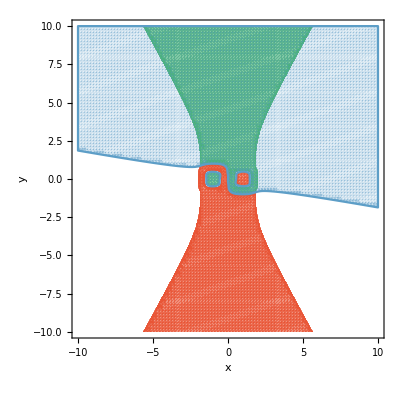

```mathematica
benchmarkname = "2d_ex2";
Print[benchmarkname];
verifytimelimit=60; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-10,10},{-10,10}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

```mathematica
benchmarkname = "2d_ex3";
Print[benchmarkname];
verifytimelimit=10; (*verification time limit*)
plot =0; (*whether to plot(=1) or not (=0)*)
plotRange = {{-4,4},{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

2d_ex3

x Variables: {x,y,z}

y Variables: {a1}

z Variables: {R,r}

S1: {{1.-x^2-y^2+0.1 z^4,-x^2-y^2+10. z^2}}

S2: {{-r^4+2. r^2 R^2-R^4+2. r^2 x^2+2. R^2 x^2-x^4+2. r^2 y^2+2. R^2 y^2-2. x^2 y^2-y^4+2. r^2 z^2-2. R^2 z^2-2. x^2 z^2-2. y^2 z^2-z^4,-4.+R,6.-R,-0.5+r,1.-r}}

Verifying results (CAV20 method)...

{}{}

Valid solution.

h2.70814-17.3401 x^2-17.3401 y^2+177.769 z^2

SDP Time: 0.196765

verify Time: 0.589923

Total Time: 0.786688

Verifying results (homogenization)...

{}{}

Valid solution.

hHomo:0.0740168-0.0878288 x^2-0.0878288 y^2+z^2

SDP Time: 0.484113

verify Time: 1.0158

Total Time: 1.49991

```mathematica
RegionPlot3D[{1+0.1*z^4-x^2-y^2≥ 0, (x^2+y^2+z^2+3^2-1^2)^2≤ 4*3^2*(x^2+y^2)},{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-